Шумы при сдвиге частот Δφ=0:
Через функции!

```mathematica
SVDVector[x_, a_?NumberQ] := Transpose[SingularValueDecomposition[x][[1; 3]]][[a]];
```

```mathematica
AbsFourier[x_]:=Abs[Take[Fourier[x,FourierParameters->{-1, 1}],{3,Round[Length[x]/2 ]+1}]]
```

```mathematica
NumPlace[x_]:=Position[AbsFourier[x],Max[AbsFourier[x]]][[1,1]]
```

```mathematica
FreqList[x_]:=Table[1.0*b/Length[x],{b,2,Length[x]-1}]
Freq[x_]:=FreqList[x][[NumPlace[x]]]
```

```mathematica
SetOptions[{Plot,ListPlot,ListLinePlot,ListLogPlot},PlotRange->Full,Axes->False,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],BaseStyle->{FontFamily->"Courier New",FontSize->12,Bold},ImageSize->600,PlotStyle->{Red,PointSize[0.01]}];
TruePlot[x_]:=ListPlot[Transpose[{FreqList[x][[NumPlace[x]-4;;NumPlace[x]+4]],AbsFourier[x][[NumPlace[x]-4;;NumPlace[x]+4]]}],FrameLabel->{"ν","A, mm"}]
FullPlot[x_]:=ListPlot[Transpose[{FreqList[x][[3;;Round[Length[x]/2 ]+1]],AbsFourier[x]}],FrameLabel->{"ν","A, mm"}]
```

```mathematica
Unprotect[Internal`EncodeCharacters];

Internal`EncodeCharacters[str_,enc_]:=Quiet[FromCharacterCode[ToCharacterCode[str],enc]]

SetDirectory[NotebookDirectory[]<>"data.06"]
```

D:\Документы\Diploma Mag\PCA\data.06

```mathematica
data1=Import["v2k_bpm_xy_1.sdds","Table","HeaderLines"->13];
data2=Import["v2k_bpm_xy_2.sdds","Table","HeaderLines"->13];
data3=Import["v2k_bpm_xy_3.sdds","Table","HeaderLines"->13];
data4=Import["v2k_bpm_xy_4.sdds","Table","HeaderLines"->13];
```

```mathematica
Data1 = Transpose[data1][[3]];
Data2 = Transpose[data2][[3]];
Data3 = Transpose[data3][[3]];
Data4 = Transpose[data4][[3]];
Data5 = Transpose[data1][[3]];
Data6 = Transpose[data2][[3]];
Data7 = Transpose[data3][[3]];
Data8 = Transpose[data4][[3]];
```

```mathematica
SigM=List[Data1,Data2,Data3,Data4, Data5, Data6, Data7, Data8];
MatrixQ[SigM]
MatrixForm[SigM]
```

True

(1)
 |  |  |  |

0.170839

0.170839

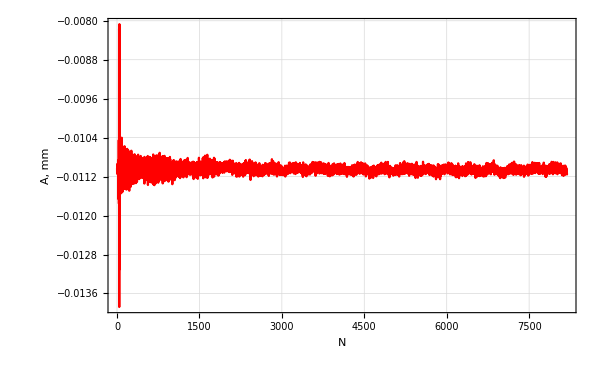

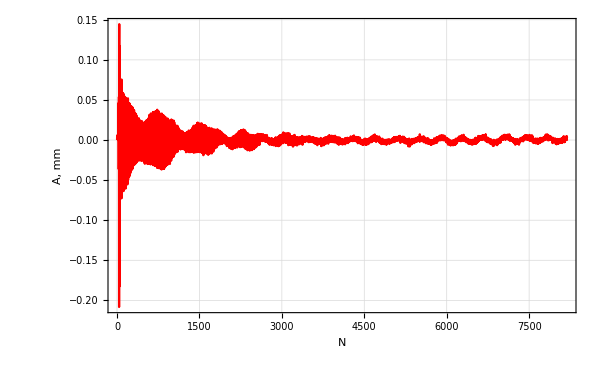

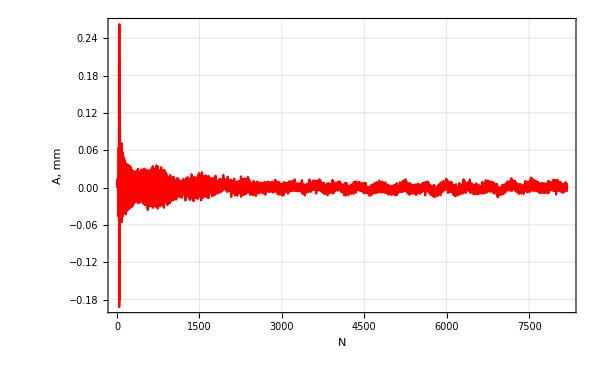

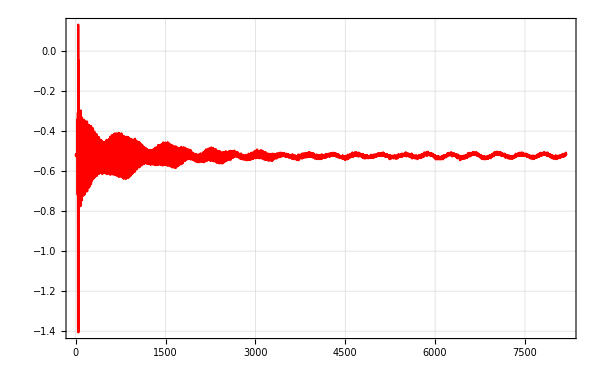

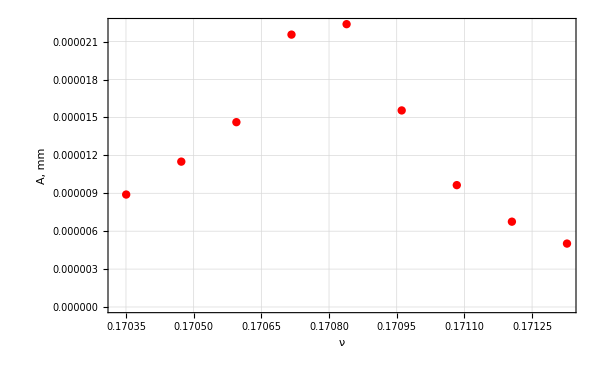

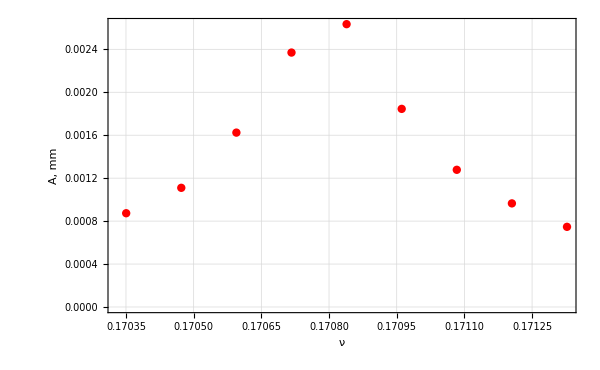

```mathematica
SVDVector1=SVDVector[SigM,1];
SVDVector2=SVDVector[SigM,2];
SVDVector3=SVDVector[SigM,3];
Freq[SVDVector1]
Freq[SVDVector3]
SVDPlot1=ListPlot[SVDVector1,Joined->True,PlotRange->All,FrameLabel->{"N","A, mm"}]
SVDPlot2=ListPlot[SVDVector2,Joined->True,PlotRange->All,FrameLabel->{"N","A, mm"}]
SVDPlot3=ListPlot[SVDVector3,Joined->True,PlotRange->All,FrameLabel->{"N","A, mm"}]

sigPlot=ListPlot[Data1,Joined->True,PlotRange->All]
TrueSVD1=TruePlot[SVDVector1]
TrueSVD3=TruePlot[SVDVector3]
```

0.170839

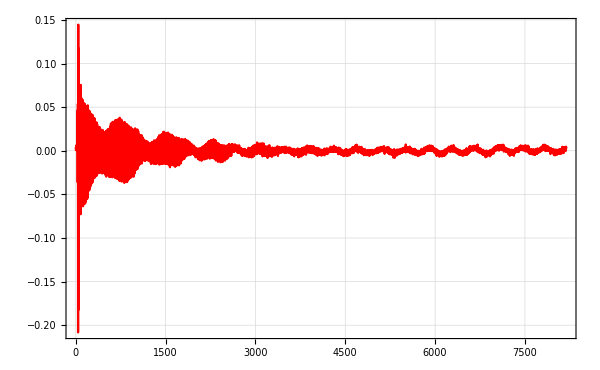

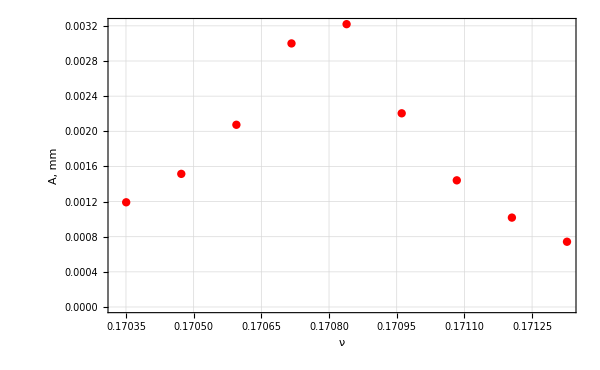

```mathematica
SVDVector2=SVDVector[SigM,2];
Freq[SVDVector2]
ListPlot[SVDVector2,Joined->True,PlotRange->All]
TrueSVD2=TruePlot[SVDVector2]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Документы\Diploma Mag\PCA

Export["SigPlot.png",sigPlot]
Export["PCA1.png",SVDPlot1]
Export["PCA2.png",SVDPlot2]
Export["PCA3.png",SVDPlot3]
Export["Spec1.png",TrueSVD1]
Export["Spec2.png",TrueSVD2]
Export["Spec3.png",TrueSVD3]

SigPlot.png

PCA1.png

PCA2.png

PCA3.png

Spec1.png

Spec2.png

Spec3.png

0.393577

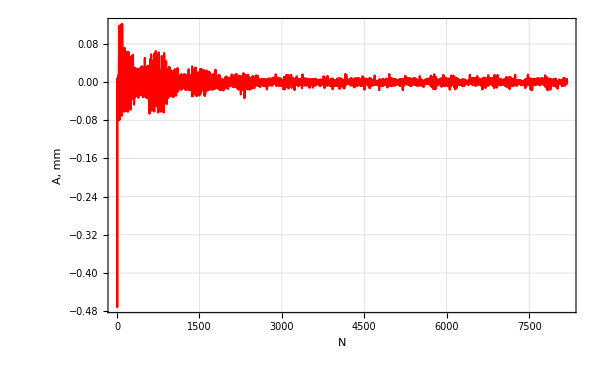

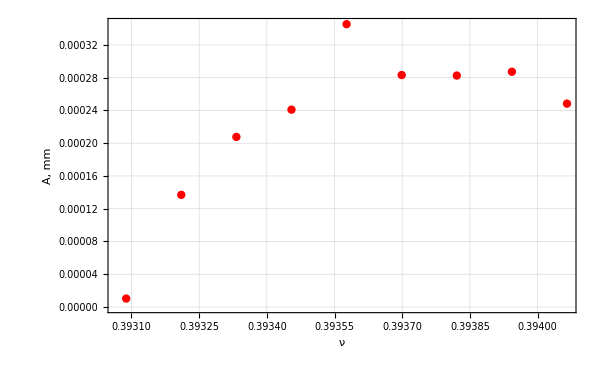

```mathematica
SVDVector7=SVDVector[SigM,7];
Freq[SVDVector7]
SVDPlot4=ListPlot[SVDVector7,Joined->True,PlotRange->All,FrameLabel->{"N","A, mm"}]
TrueSVD4=TruePlot[SVDVector7]
```

```mathematica
Export["SVDPlot4.png",SVDPlot4]
Export["TrueSVD4.png",TrueSVD4]
```

SVDPlot4.png

TrueSVD4.png

0.170839

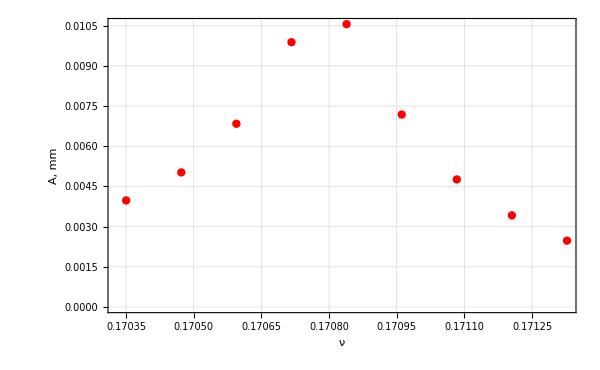

```mathematica
Freq[Data1]
Truesig=TruePlot[Data1]
```

```mathematica
Export["Truesig.png",Truesig]
```

Truesig.png

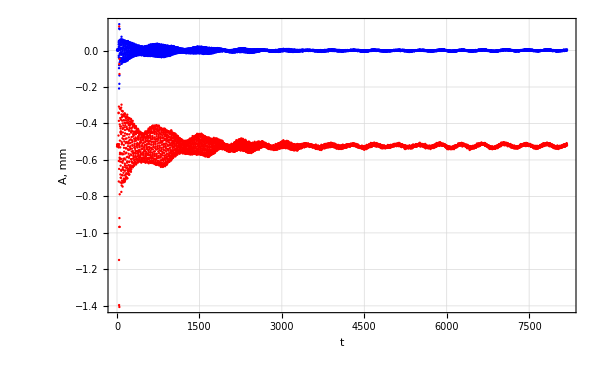

```mathematica
DobPCA=ListPlot[{SVDVector2,Data1},PlotStyle->{Blue,Red},FrameLabel->{"t","A, mm"}]
```

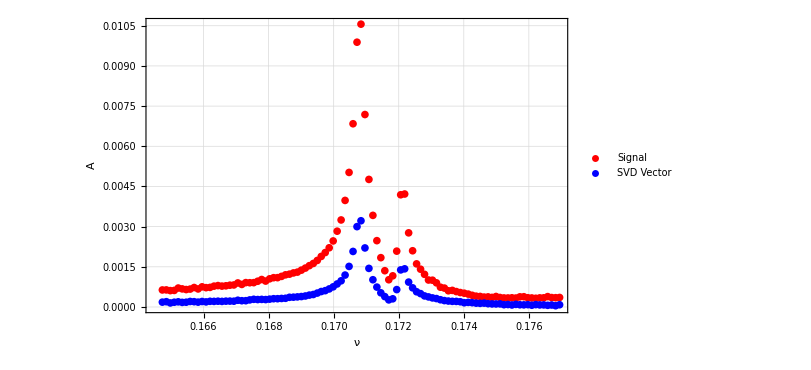

```mathematica
FulMasSig=Transpose[{FreqList[Data1][[NumPlace[Data1]-50;;NumPlace[Data1]+50]],AbsFourier[Data1][[NumPlace[Data1]-50;;NumPlace[Data1]+50]]}];
FulMasSVD2 =Transpose[{FreqList[SVDVector2][[NumPlace[SVDVector2]-50;;NumPlace[SVDVector2]+50]],AbsFourier[SVDVector2][[NumPlace[SVDVector2]-50;;NumPlace[SVDVector2]+50]]}];
DobFourPCA=ListPlot[{FulMasSig,FulMasSVD2},PlotStyle->{Red,Blue}, PlotLegends->Placed[{"Signal","SVD Vector"},{Scaled[{0.95,0.7}],{0.95,0.7}}],FrameLabel->{"ν","A"}]
```

```mathematica
Export["DobFourPCA.png",DobFourPCA]
```

DobFourPCA.png

```mathematica
Export["DobPCA.png",DobPCA]
```

DobPCA.png